```mathematica
SetDirectory["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Figuras"]
```

C:\Users\danal\Documents\GitHub\Tesis-de-Licenciatura\Figuras

0.668652

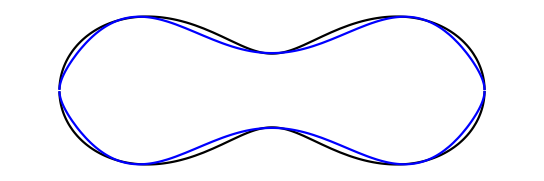

```mathematica
a2=2.6576799092522765;

(*Ecuacion Cassini con c*)
z1[x_,a_,R_]:=(0.71/Sqrt[R^2- 2a ^2])(-a^2-x^2+(4 x^2 a^2+(R^2-a ^2)^2)^(1/2))^(1/2)

(*Ecuación Tsang*)
zT[x_,R_]:=((1-(x/R)^2)^(0.5))*(0.72+4.152*(x/R)^2-3.426*(x/R)^4)

(*grafica*)
comparacionGeometrias=Plot[{Style[z1[x,a2,3.825],Black],Style[-z1[x,a2,3.825],Black],Style[zT[x],Blue],Style[-zT[x,3.825],Blue]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

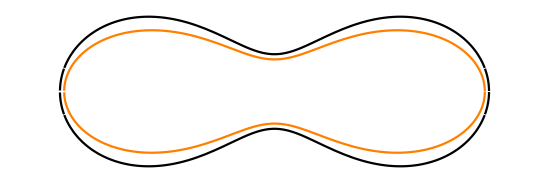

```mathematica
(*Ecuacion Cassini  sin c*)
cassini[x_,a_,R_]:=(-a^2-x^2+(4 x^2 a^2+(R^2-a ^2)^2)^(1/2))^(1/2)


(*Ecuacion Cassini con c*)
z1[x_,a_,c_,R_]:=c(-a^2-x^2+(4 x^2 a^2+(R^2-a ^2)^2)^(1/2))^(1/2)
comparacionGeometrias=Plot[{Style[cassini[x,a2,3.825],Black],Style[-cassini[x,a2,3.825],Black],Style[z1[x,2.6,0.83,3.75],Orange],Style[-z1[x,2.6,0.83,3.75],Orange]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

```mathematica
3.825*0.8
```

3.06

```mathematica
a2*0.9
3.825*0.9
```

2.39191

3.4425

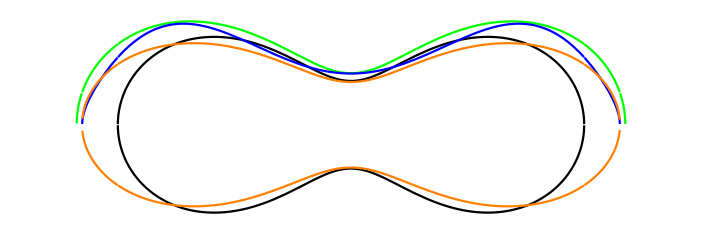

```mathematica
z1[x_,a_,c_,R_]:=c(-a^2-x^2+(4 x^2 a^2+(R^2-a ^2)^2)^(1/2))^(1/2)
comparacionGeometrias=Plot[{Style[cassini[x,a2*0.85,3.825*0.85],Black],Style[-cassini[x,a2*0.85,3.825*0.85],Black],Style[z1[x,a2,1,3.825],Green],Style[zT[x,3.825*0.98]*0.98,Blue],Style[z1[x,2.6,0.8,3.75],Orange],Style[-z1[x,2.6,0.8,3.75],Orange]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

```mathematica
MaximalBy[Table[{x,z1[x,a2*0.98,0.98,3.825*0.98]},{x,0,3.75,0.01}],Last]
```

{{2.2,1.3673}}

```mathematica
MaximalBy[Table[{x,z1[x,2.6,0.8,3.75]},{x,0,3.75,0.01}],Last]
MaximalBy[Table[{x,cassini[x,a2,3.825]},{x,0,3.75,0.01}],Last]
z1[0,2.6,0.8,3.75]
cassini[0,a2,3.825]
```

{{2.19,1.12346}}

{{2.24,1.42367}}

0.589237

0.71

```mathematica
Table[{x,cassini[x,2.6,3.75]},{x,0,3.75,0.01}]
```

{{0.,0.736546},{0.01,0.736604},{0.02,0.736777},{0.03,0.737066},{0.04,0.73747},{0.05,0.737989},{0.06,0.738622},{0.07,0.739369},{0.08,0.740229},{0.09,0.741202},{0.1,0.742288},{0.11,0.743484},{0.12,0.74479},{0.13,0.746205},{0.14,0.747729},{0.15,0.749359},{0.16,0.751095},{0.17,0.752935},{0.18,0.754879},{0.19,0.756924},{0.2,0.759069},{0.21,0.761312},{0.22,0.763653},{0.23,0.766089},{0.24,0.768618},{0.25,0.77124},{0.26,0.773952},{0.27,0.776752},{0.28,0.779639},{0.29,0.78261},{0.3,0.785665},{0.31,0.7888},{0.32,0.792014},{0.33,0.795305},{0.34,0.798672},{0.35,0.802111},{0.36,0.805622},{0.37,0.809202},{0.38,0.812849},{0.39,0.816561},{0.4,0.820336},{0.41,0.824172},{0.42,0.828068},{0.43,0.832021},{0.44,0.83603},{0.45,0.840091},{0.46,0.844204},{0.47,0.848367},{0.48,0.852577},{0.49,0.856833},{0.5,0.861132},{0.51,0.865474},{0.52,0.869855},{0.53,0.874275},{0.54,0.878732},{0.55,0.883223},{0.56,0.887747},{0.57,0.892303},{0.58,0.896888},{0.59,0.901501},{0.6,0.90614},{0.61,0.910804},{0.62,0.915491},{0.63,0.920199},{0.64,0.924928},{0.65,0.929675},{0.66,0.934438},{0.67,0.939218},{0.68,0.944011},{0.69,0.948817},{0.7,0.953634},{0.71,0.958461},{0.72,0.963297},{0.73,0.96814},{0.74,0.97299},{0.75,0.977843},{0.76,0.982701},{0.77,0.987561},{0.78,0.992422},{0.79,0.997283},{0.8,1.00214},{0.81,1.007},{0.82,1.01186},{0.83,1.01671},{0.84,1.02155},{0.85,1.02639},{0.86,1.03122},{0.87,1.03605},{0.88,1.04086},{0.89,1.04566},{0.9,1.05046},{0.91,1.05524},{0.92,1.06001},{0.93,1.06476},{0.94,1.0695},{0.95,1.07423},{0.96,1.07894},{0.97,1.08363},{0.98,1.08831},{0.99,1.09297},{1.,1.09761},{1.01,1.10222},{1.02,1.10682},{1.03,1.1114},{1.04,1.11596},{1.05,1.1205},{1.06,1.12501},{1.07,1.1295},{1.08,1.13396},{1.09,1.1384},{1.1,1.14282},{1.11,1.14721},{1.12,1.15158},{1.13,1.15592},{1.14,1.16023},{1.15,1.16451},{1.16,1.16877},{1.17,1.173},{1.18,1.17719},{1.19,1.18136},{1.2,1.1855},{1.21,1.18961},{1.22,1.19369},{1.23,1.19774},{1.24,1.20176},{1.25,1.20575},{1.26,1.2097},{1.27,1.21362},{1.28,1.21751},{1.29,1.22137},{1.3,1.22519},{1.31,1.22898},{1.32,1.23273},{1.33,1.23645},{1.34,1.24014},{1.35,1.24379},{1.36,1.2474},{1.37,1.25098},{1.38,1.25453},{1.39,1.25803},{1.4,1.26151},{1.41,1.26494},{1.42,1.26834},{1.43,1.2717},{1.44,1.27502},{1.45,1.27831},{1.46,1.28156},{1.47,1.28477},{1.48,1.28794},{1.49,1.29107},{1.5,1.29417},{1.51,1.29722},{1.52,1.30024},{1.53,1.30322},{1.54,1.30616},{1.55,1.30906},{1.56,1.31191},{1.57,1.31473},{1.58,1.31751},{1.59,1.32025},{1.6,1.32294},{1.61,1.3256},{1.62,1.32822},{1.63,1.33079},{1.64,1.33332},{1.65,1.33581},{1.66,1.33826},{1.67,1.34067},{1.68,1.34303},{1.69,1.34536},{1.7,1.34764},{1.71,1.34988},{1.72,1.35207},{1.73,1.35423},{1.74,1.35633},{1.75,1.3584},{1.76,1.36043},{1.77,1.36241},{1.78,1.36434},{1.79,1.36623},{1.8,1.36808},{1.81,1.36989},{1.82,1.37165},{1.83,1.37336},{1.84,1.37504},{1.85,1.37666},{1.86,1.37825},{1.87,1.37978},{1.88,1.38128},{1.89,1.38272},{1.9,1.38412},{1.91,1.38548},{1.92,1.38679},{1.93,1.38806},{1.94,1.38927},{1.95,1.39045},{1.96,1.39157},{1.97,1.39265},{1.98,1.39369},{1.99,1.39467},{2.,1.39561},{2.01,1.3965},{2.02,1.39735},{2.03,1.39815},{2.04,1.3989},{2.05,1.3996},{2.06,1.40026},{2.07,1.40086},{2.08,1.40142},{2.09,1.40193},{2.1,1.40239},{2.11,1.4028},{2.12,1.40317},{2.13,1.40348},{2.14,1.40375},{2.15,1.40396},{2.16,1.40413},{2.17,1.40424},{2.18,1.40431},{2.19,1.40433},{2.2,1.40429},{2.21,1.40421},{2.22,1.40407},{2.23,1.40388},{2.24,1.40364},{2.25,1.40335},{2.26,1.40301},{2.27,1.40262},{2.28,1.40217},{2.29,1.40167},{2.3,1.40112},{2.31,1.40052},{2.32,1.39986},{2.33,1.39915},{2.34,1.39838},{2.35,1.39757},{2.36,1.39669},{2.37,1.39577},{2.38,1.39479},{2.39,1.39375},{2.4,1.39266},{2.41,1.39151},{2.42,1.39031},{2.43,1.38905},{2.44,1.38773},{2.45,1.38636},{2.46,1.38493},{2.47,1.38344},{2.48,1.38189},{2.49,1.38029},{2.5,1.37863},{2.51,1.37691},{2.52,1.37513},{2.53,1.37329},{2.54,1.37139},{2.55,1.36943},{2.56,1.36741},{2.57,1.36533},{2.58,1.36318},{2.59,1.36098},{2.6,1.35871},{2.61,1.35638},{2.62,1.35399},{2.63,1.35153},{2.64,1.34901},{2.65,1.34642},{2.66,1.34377},{2.67,1.34105},{2.68,1.33827},{2.69,1.33542},{2.7,1.3325},{2.71,1.32951},{2.72,1.32646},{2.73,1.32333},{2.74,1.32014},{2.75,1.31688},{2.76,1.31354},{2.77,1.31014},{2.78,1.30666},{2.79,1.30311},{2.8,1.29948},{2.81,1.29578},{2.82,1.29201},{2.83,1.28815},{2.84,1.28423},{2.85,1.28022},{2.86,1.27614},{2.87,1.27198},{2.88,1.26773},{2.89,1.26341},{2.9,1.259},{2.91,1.25451},{2.92,1.24994},{2.93,1.24528},{2.94,1.24054},{2.95,1.23571},{2.96,1.23079},{2.97,1.22578},{2.98,1.22068},{2.99,1.21549},{3.,1.2102},{3.01,1.20482},{3.02,1.19935},{3.03,1.19378},{3.04,1.18811},{3.05,1.18233},{3.06,1.17646},{3.07,1.17049},{3.08,1.1644},{3.09,1.15822},{3.1,1.15192},{3.11,1.14551},{3.12,1.13899},{3.13,1.13236},{3.14,1.12561},{3.15,1.11874},{3.16,1.11175},{3.17,1.10463},{3.18,1.09739},{3.19,1.09002},{3.2,1.08252},{3.21,1.07489},{3.22,1.06711},{3.23,1.0592},{3.24,1.05114},{3.25,1.04294},{3.26,1.03459},{3.27,1.02608},{3.28,1.01742},{3.29,1.00859},{3.3,0.999592},{3.31,0.990426},{3.32,0.981083},{3.33,0.971559},{3.34,0.961848},{3.35,0.951944},{3.36,0.941841},{3.37,0.931533},{3.38,0.921012},{3.39,0.910271},{3.4,0.899303},{3.41,0.888098},{3.42,0.876647},{3.43,0.864941},{3.44,0.852969},{3.45,0.840719},{3.46,0.828179},{3.47,0.815336},{3.48,0.802175},{3.49,0.78868},{3.5,0.774834},{3.51,0.760616},{3.52,0.746007},{3.53,0.730981},{3.54,0.715513},{3.55,0.699574},{3.56,0.683131},{3.57,0.666145},{3.58,0.648574},{3.59,0.63037},{3.6,0.611475},{3.61,0.591824},{3.62,0.571338},{3.63,0.549923},{3.64,0.527467},{3.65,0.50383},{3.66,0.478837},{3.67,0.452263},{3.68,0.423812},{3.69,0.393075},{3.7,0.359465},{3.71,0.322086},{3.72,0.279429},{3.73,0.228555},{3.74,0.161897},{3.75,0.}}

{{0.,0.351141},{0.01,0.351278},{0.02,0.35169},{0.03,0.352375},{0.04,0.353332},{0.05,0.354558},{0.06,0.35605},{0.07,0.357803},{0.08,0.359814},{0.09,0.362078},{0.1,0.364589},{0.11,0.367341},{0.12,0.370328},{0.13,0.373544},{0.14,0.376981},{0.15,0.380632},{0.16,0.38449},{0.17,0.388548},{0.18,0.392798},{0.19,0.397232},{0.2,0.401844},{0.21,0.406625},{0.22,0.411568},{0.23,0.416665},{0.24,0.42191},{0.25,0.427296},{0.26,0.432814},{0.27,0.43846},{0.28,0.444225},{0.29,0.450105},{0.3,0.456091},{0.31,0.462179},{0.32,0.468362},{0.33,0.474636},{0.34,0.480994},{0.35,0.487431},{0.36,0.493942},{0.37,0.500522},{0.38,0.507168},{0.39,0.513873},{0.4,0.520635},{0.41,0.527448},{0.42,0.534309},{0.43,0.541214},{0.44,0.548159},{0.45,0.555141},{0.46,0.562156},{0.47,0.569202},{0.48,0.576274},{0.49,0.583371},{0.5,0.59049},{0.51,0.597626},{0.52,0.604779},{0.53,0.611945},{0.54,0.619122},{0.55,0.626308},{0.56,0.633501},{0.57,0.640698},{0.58,0.647897},{0.59,0.655096},{0.6,0.662294},{0.61,0.669489},{0.62,0.676679},{0.63,0.683862},{0.64,0.691036},{0.65,0.698201},{0.66,0.705354},{0.67,0.712495},{0.68,0.719622},{0.69,0.726733},{0.7,0.733827},{0.71,0.740904},{0.72,0.747961},{0.73,0.754999},{0.74,0.762015},{0.75,0.769008},{0.76,0.775979},{0.77,0.782925},{0.78,0.789846},{0.79,0.796741},{0.8,0.803608},{0.81,0.810448},{0.82,0.81726},{0.83,0.824042},{0.84,0.830794},{0.85,0.837515},{0.86,0.844205},{0.87,0.850862},{0.88,0.857487},{0.89,0.864079},{0.9,0.870636},{0.91,0.877159},{0.92,0.883647},{0.93,0.890099},{0.94,0.896515},{0.95,0.902894},{0.96,0.909236},{0.97,0.915541},{0.98,0.921808},{0.99,0.928036},{1.,0.934225},{1.01,0.940376},{1.02,0.946486},{1.03,0.952557},{1.04,0.958587},{1.05,0.964577},{1.06,0.970526},{1.07,0.976433},{1.08,0.982299},{1.09,0.988123},{1.1,0.993905},{1.11,0.999645},{1.12,1.00534},{1.13,1.011},{1.14,1.01661},{1.15,1.02217},{1.16,1.0277},{1.17,1.03318},{1.18,1.03861},{1.19,1.044},{1.2,1.04935},{1.21,1.05465},{1.22,1.05991},{1.23,1.06512},{1.24,1.07029},{1.25,1.07541},{1.26,1.08049},{1.27,1.08552},{1.28,1.09051},{1.29,1.09545},{1.3,1.10034},{1.31,1.10519},{1.32,1.10999},{1.33,1.11474},{1.34,1.11945},{1.35,1.12411},{1.36,1.12873},{1.37,1.13329},{1.38,1.13781},{1.39,1.14229},{1.4,1.14671},{1.41,1.15109},{1.42,1.15543},{1.43,1.15971},{1.44,1.16395},{1.45,1.16814},{1.46,1.17228},{1.47,1.17637},{1.48,1.18042},{1.49,1.18442},{1.5,1.18837},{1.51,1.19227},{1.52,1.19613},{1.53,1.19993},{1.54,1.20369},{1.55,1.2074},{1.56,1.21106},{1.57,1.21468},{1.58,1.21824},{1.59,1.22176},{1.6,1.22522},{1.61,1.22864},{1.62,1.23201},{1.63,1.23533},{1.64,1.23861},{1.65,1.24183},{1.66,1.245},{1.67,1.24813},{1.68,1.25121},{1.69,1.25423},{1.7,1.25721},{1.71,1.26014},{1.72,1.26302},{1.73,1.26585},{1.74,1.26863},{1.75,1.27137},{1.76,1.27405},{1.77,1.27668},{1.78,1.27926},{1.79,1.2818},{1.8,1.28428},{1.81,1.28671},{1.82,1.2891},{1.83,1.29143},{1.84,1.29371},{1.85,1.29595},{1.86,1.29813},{1.87,1.30026},{1.88,1.30235},{1.89,1.30438},{1.9,1.30636},{1.91,1.30829},{1.92,1.31017},{1.93,1.312},{1.94,1.31378},{1.95,1.31551},{1.96,1.31719},{1.97,1.31882},{1.98,1.32039},{1.99,1.32192},{2.,1.32339},{2.01,1.32481},{2.02,1.32618},{2.03,1.3275},{2.04,1.32877},{2.05,1.32998},{2.06,1.33114},{2.07,1.33226},{2.08,1.33331},{2.09,1.33432},{2.1,1.33528},{2.11,1.33618},{2.12,1.33703},{2.13,1.33782},{2.14,1.33857},{2.15,1.33926},{2.16,1.33989},{2.17,1.34048},{2.18,1.34101},{2.19,1.34148},{2.2,1.34191},{2.21,1.34228},{2.22,1.34259},{2.23,1.34285},{2.24,1.34306},{2.25,1.34321},{2.26,1.34331},{2.27,1.34335},{2.28,1.34334},{2.29,1.34327},{2.3,1.34315},{2.31,1.34297},{2.32,1.34273},{2.33,1.34244},{2.34,1.34209},{2.35,1.34169},{2.36,1.34123},{2.37,1.34071},{2.38,1.34013},{2.39,1.3395},{2.4,1.33881},{2.41,1.33806},{2.42,1.33725},{2.43,1.33639},{2.44,1.33547},{2.45,1.33448},{2.46,1.33344},{2.47,1.33234},{2.48,1.33118},{2.49,1.32995},{2.5,1.32867},{2.51,1.32733},{2.52,1.32592},{2.53,1.32446},{2.54,1.32293},{2.55,1.32134},{2.56,1.31968},{2.57,1.31797},{2.58,1.31619},{2.59,1.31435},{2.6,1.31244},{2.61,1.31047},{2.62,1.30843},{2.63,1.30633},{2.64,1.30416},{2.65,1.30192},{2.66,1.29962},{2.67,1.29725},{2.68,1.29482},{2.69,1.29231},{2.7,1.28974},{2.71,1.2871},{2.72,1.28438},{2.73,1.2816},{2.74,1.27875},{2.75,1.27582},{2.76,1.27282},{2.77,1.26975},{2.78,1.26661},{2.79,1.26339},{2.8,1.26009},{2.81,1.25672},{2.82,1.25328},{2.83,1.24976},{2.84,1.24616},{2.85,1.24248},{2.86,1.23872},{2.87,1.23488},{2.88,1.23096},{2.89,1.22696},{2.9,1.22288},{2.91,1.21871},{2.92,1.21446},{2.93,1.21012},{2.94,1.20569},{2.95,1.20118},{2.96,1.19658},{2.97,1.19189},{2.98,1.1871},{2.99,1.18223},{3.,1.17726},{3.01,1.1722},{3.02,1.16704},{3.03,1.16178},{3.04,1.15642},{3.05,1.15096},{3.06,1.14541},{3.07,1.13974},{3.08,1.13397},{3.09,1.1281},{3.1,1.12211},{3.11,1.11602},{3.12,1.10981},{3.13,1.10349},{3.14,1.09705},{3.15,1.09049},{3.16,1.08382},{3.17,1.07702},{3.18,1.07009},{3.19,1.06303},{3.2,1.05585},{3.21,1.04853},{3.22,1.04107},{3.23,1.03347},{3.24,1.02573},{3.25,1.01785},{3.26,1.00981},{3.27,1.00162},{3.28,0.993277},{3.29,0.984769},{3.3,0.976096},{3.31,0.967252},{3.32,0.958234},{3.33,0.949035},{3.34,0.939651},{3.35,0.930075},{3.36,0.920302},{3.37,0.910326},{3.38,0.900139},{3.39,0.889734},{3.4,0.879104},{3.41,0.868239},{3.42,0.857131},{3.43,0.845771},{3.44,0.834147},{3.45,0.822249},{3.46,0.810065},{3.47,0.797581},{3.48,0.784782},{3.49,0.771654},{3.5,0.758178},{3.51,0.744337},{3.52,0.730108},{3.53,0.71547},{3.54,0.700395},{3.55,0.684855},{3.56,0.668818},{3.57,0.652247},{3.58,0.6351},{3.59,0.617329},{3.6,0.598878},{3.61,0.579682},{3.62,0.559665},{3.63,0.538734},{3.64,0.516779},{3.65,0.493663},{3.66,0.469214},{3.67,0.443212},{3.68,0.415364},{3.69,0.385271},{3.7,0.352358},{3.71,0.315744},{3.72,0.273948},{3.73,0.22409},{3.74,0.158747},{3.75,0.}}

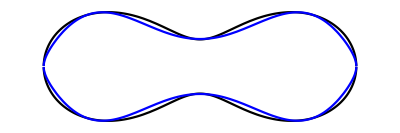

```mathematica
comparacionGeometrias=Plot[{Style[cassini[x,a2,3.825],Black],Style[-cassini[x,a2,3.825],Black],Style[zT[x],Blue],Style[zT2[x],Blue]},{x,-4,4},AspectRatio->1/3,Axes->False]
```

```mathematica
Export["comparacion_geom_eri.svg",comparacionGeometrias]
```

comparacion_geom_eri.svg

```mathematica
(*Ajuste de Cassini a Tsang*)
```

```mathematica
data=Table[zT[x],{x,-3.82,3.82}]
```

{0.0742706,1.32732,1.30561,0.882575,0.72837,1.03124,1.40278,1.08536}

```mathematica
nlm=NonlinearModelFit[data,{cassini[x,a,3.825],cassini[0,a,3.825]==0.72},{{a,2.65}},x]
```

NonlinearModelFit::nrnum: The function value -27.3764-17.1876 ⅈ is not a real number at {a} = {2.65}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {a} = {2.65}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{x={1.,2.,3.,4.,5.,6.,7.,8.},Optimization`FindFit`y$550853={0.0742706,1.32732,1.30561,0.882575,0.72837,1.03124,1.40278,1.08536}},1/2 Block[{«3»},Subtract[«2»]].Block[{«3»},Subtract[«2»]]]],Block},{0,{{{},1,0,Hold[a],0,0}}},«3»,{None,None,None}] failed at {2.65}.

NonlinearModelFit::nrnum: The function value -27.3764-17.1876 ⅈ is not a real number at {a} = {2.65}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {a} = {2.65}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{x={1.,2.,3.,4.,5.,6.,7.,8.},Optimization`FindFit`y$550943={0.0742706,1.32732,1.30561,0.882575,0.72837,1.03124,1.40278,1.08536}},1/2 Block[{«3»},Subtract[«2»]].Block[{«3»},Subtract[«2»]]]],Block},{0,{{{},1,0,Hold[a],0,0}}},«3»,{None,None,None}] failed at {2.65}.

NonlinearModelFit[{0.0742706,1.32732,1.30561,0.882575,0.72837,1.03124,1.40278,1.08536},{√(-a^2-x^2+√((14.6306-a^2)^2+4 a^2 x^2)),√(-a^2+√((14.6306-a^2)^2))==0.72},{{a,2.65}},x]

```mathematica
nlm["BestFitParameters"]
```

{a→2.65768}

```mathematica
(*Cálculo de volúmenes*)
```

```mathematica
s[a_]:=4 Pi NIntegrate[x Sqrt[(-a^2-x^2+(4 x^2 a^2+(3.825^2-a ^2)^2)^(1/2))],{x,0,3.825}]
micro[a_,x_]:=4 Pi NIntegrate[x Sqrt[(-a^2-x^2+(4 x^2 a^2+((3.825/1.5)^2-a ^2)^2)^(1/2))],{x,0,3.825/1.5}]
menor[a_,x_]:=4 Pi NIntegrate[x Sqrt[(-a^2-x^2+(4 x^2 a^2+((3.825*0.95)^2-a ^2)^2)^(1/2))],{x,0,3.825*0.95}]
V=4 Pi NIntegrate[rho*zT[rho],{rho,0,3.825}]
A=4 Pi NIntegrate[r*Sqrt[1+(zT'[r])^2],{r,0,3.825}]
s[a2]
micro[a2/1.5]
s[a2]/menor[a2*0.95]
```

97.9153

126.548

104.788

31.0484

1.16635

```mathematica
3.825*0.95
a2*0.95
```

3.63375

2.5248

44.2076

```mathematica
4 Pi NIntegrate[x Sqrt[(-a2^2-x^2+(4 x^2 a2^2+(3.825^2-a2 ^2)^2)^(1/2))],{x,0,3.825}]
```

```mathematica
((s[a2])*3/(4 Pi))^(1/3)
```

2.92466

```mathematica
s[a2]
```

```mathematica
N[((86)*3/(4 Pi))^(1/3)]
```

2.73823

```mathematica
a2/1.5
```

1.77179

```mathematica
cassinieri[x_]:=cassini[x,a2,3.825]
```

```mathematica
max=GoldenSearchMax[cassinieri, #1, #2, 0.0005] & @@@ {{-3.825,0},{0,3.825}}
GoldenSearchMax[zT, #1, #2, 0.0005] & @@@ {{-3.825,0},{0,3.825}}
```

{-2.24432,2.24432}

{-2.3858,2.3858}

```mathematica
cassinieri[2.244323480268809]*2
zT[2.3858003105123915]*2
```

2.84736

2.8401